# CR3BP

The ODEs are 
	x'' | - | 2y' | = | x | - | (1-η)(x + η)/(ρ_1)^3 | - | η(x - 1 + η)/(ρ_2)^3
y'' | + | 2x' | = | y | - | (1-η)y/(ρ_1)^3 | - | η y/(ρ_2)^3
where 
	ρ_1^2=(x+η)^2+y^2
ρ_2^2=(x-1+η)^2+y^2 
This is sometimes written in terms of ∂_x Ω and ∂_y Ω_y where
	Ω(x,y)=1/2(x^2+y^2)+(1-η)/ρ_1+η/ρ_2    
This is easy enough to enter and solve.  I am going to do this as a second order system and as a first order system.

### Second Order System

This is a test to make sure I implemented things correctly! 
I know what this solution should look like.  
The “duration” is a little under 2π≈6.283185307179586

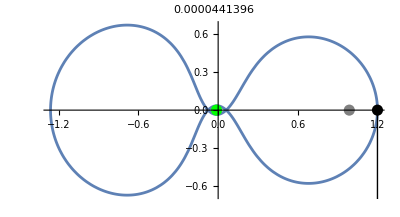

```mathematica
η=1/82.45;
vy0=-1.049357509830320; x0=1.2;
TMax=6.1922169331319640;
{xSol,ySol}=NDSolveValue[{
ρ1=√((x[t]+η)^2+y[t]^2); ρ2=√((x[t]-1+η)^2+y[t]^2);
x''[t]-2y'[t]==x[t]-(1-η)(x[t]+η)/ρ1^3-η (x[t]-1+η)/ρ2^3,
y''[t]+2x'[t]==y[t]-(1-η)y[t]/ρ1^3-η y[t]/ρ2^3,
x[0]==1.2, x'[0]==0,
y[0]==0,y'[0]==vy0
},
{x,y},{t, 0, TMax}];
ParametricPlot[{xSol[t],ySol[t]},{t,0, TMax},
PlotLabel->Norm[{x0-xSol[TMax],0-ySol[TMax]}],
Epilog->{PointSize[0.02],
{Gray, Point[{1-η,0}]},
{Green,Point[{-η,0}]},
{Point[{x0,0}],Arrow[{{x0,0},{x0,0}+{0,vy0}}]}
},
PlotRange->1.1{{-x0,x0},{-vy0,vy0}}
]
```

```mathematica
xSol[TMax]
```

1.20159

### First Order System

InterpolatingFunction[…]

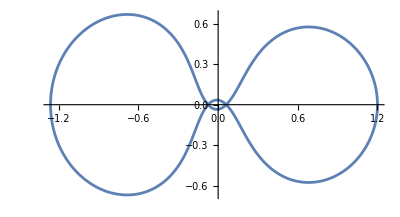

```mathematica
vy0=-1.049357509830320; x0=1.2;
TMax=6.1922169331319640;
f[{x_,y_,vx_,vy_}]:=Module[{ρ1,ρ2,η=1/82.45},
ρ1=√((x+η)^2+y^2); ρ2=√((x-1+η)^2+y^2);
{vx,vy,
2 vy+x-(1-η)(x+η)/ρ1^3-η (x-1+η)/ρ2^3,
-2 vx+y-(1-η)y/ρ1^3-η y/ρ2^3}
]
zSol=NDSolveValue[{z'[t]==f[z[t]],z[0]=={x0,0,0,vy0}},z,{t, 0, TMax}]
ParametricPlot[zSol[t]⟦{1,2}⟧,{t,0, TMax}]
```

### Lagrange Points: Where and What?

Equilibrium point (called Lagrange points) satisfy
	ρ1=√((x+η)^2+y^2); ρ2=√((x-1+η)^2+y^2);
0==x-(1-η)(x+η)/ρ1^3-η (x-1+η)/ρ2^3,
0==y-(1-η)y/ρ1^3-η y/ρ2^3

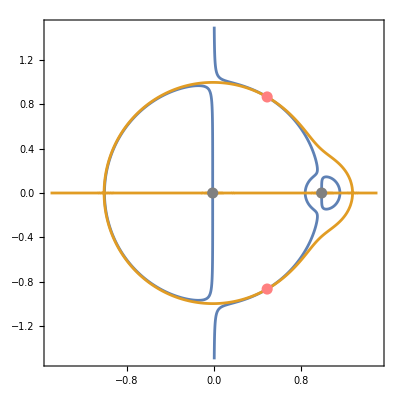

```mathematica
eq[η_][{x_,y_}]:=Module[{ρ1,ρ2},
ρ1=√((x+η)^2+y^2); ρ2=√((x-1+η)^2+y^2);
{x-(1-η)(x+η)/ρ1^3-η (x-1+η)/ρ2^3,y-(1-η)y/ρ1^3-η y/ρ2^3}]
η=1/82.45;
ContourPlot[{eq[η][{x,y}]⟦1⟧==0,eq[η][{x,y}]⟦2⟧==0},
{x,-1.5,1.5},{y,-1.5,1.5},PlotPoints->100,
Epilog->{PointSize[0.02],
{Gray, Point[{-η,0}],Point[{1-η,0}]},
{Pink, Point[{0.5-η,√3/2}],Point[{0.5-η,-√3/2}]}
}]
```

The points on the x-axis are given by the roots of the following
	x- ((1-η)(x+η))/Abs[x+η]^3- (η(x-1+η))/Abs[x-1+η]^3==0

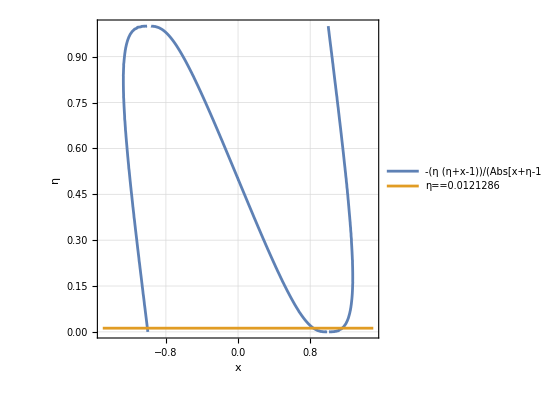

```mathematica
Clear[η]
ContourPlot[{x- ((1-η)(x+η))/Abs[x+η]^3- (η(x-1+η))/Abs[x-1+η]^3==0,η==1/82.45},{x,-1.5,1.5},{η,0,1.0},
GridLines->Automatic, FrameLabel->{"x","η"},
PlotLegends->"Expressions"]
```

### Lagrange Points: Stability?

The easiest way to see stability (or instability) is to plot solutions! First compute the equilibrium and check that they are correct!

```mathematica
f[{x_,y_,vx_,vy_}]:=Module[{ρ1,ρ2,η=1/82.45},
ρ1=√((x+η)^2+y^2); ρ2=√((x-1+η)^2+y^2);
{vx,vy,
2 vy+x-(1-η)(x+η)/ρ1^3-η (x-1+η)/ρ2^3,
-2 vx+y-(1-η)y/ρ1^3-η y/ρ2^3}
]
η=1/82.45;
L4 ={0.5-η,√3/2,0,0} ;L5={0.5-η,-√3/2,0,0};
L1 = {x,0,0,0}/.FindRoot[ f[{x,0,0,0}]⟦3⟧==0,{x, -1}];
L2 = {x,0,0,0}/.FindRoot[ f[{x,0,0,0}]⟦3⟧==0,{x, 0.5}];
L3 = {x,0,0,0}/.FindRoot[ f[{x,0,0,0}]⟦3⟧==0,{x, 1.5}];
{f[L1],f[L2],f[L3],f[L4],f[L5]}
```

{{0,0,0.,0.},{0,0,1.11022×10^-15,0.},{0,0,-2.22045×10^-16,0.},{0,0,-5.55112×10^-17,0.},{0,0,-5.55112×10^-17,0.}}

Lets look at solutions near equilibria

```mathematica
ϵ=0.01;TMax=123;
y0=L4+ϵ RandomReal[{-1,1},4];
ySol=NDSolveValue[{y'[t]==f[y[t]],y[0]==y0},y,{t,0, TMax}];
TabView[{
"2D"->ParametricPlot[ySol[t]⟦{1,2}⟧,{t,0, TMax},AxesLabel->{"x","y"}],
"1D"->Plot[{ySol[t]⟦1⟧,ySol[t]⟦2⟧},{t,0, TMax},AxesLabel->{"t",None},PlotLegends->Automatic]
}]
```

12

### Lagrange Points: Linearization?

The stability of an equilibrium point f(y^*)=0 of an ODE y'=f(y) is determined by examining the evolution of a perturbation y(t)=y^*+dy(t) starting at dy(0).  Linearization makes this process straightforward for sufficiently smooth f:ℝ^n→ℝ^n near y^*.
First plug into the ODE and expand
	(y^*)'+dy'(t)=f(y^*+dy(t))=f(y^*)+Df(y^*) dy(t)+1/2 D^2 f(y^*)(dy(t))^2…
Since y^* is constant and  f(y^*)=0 we have 
	dy'(t)=Df(y^*) dy(t)+O((dy(t))^2)
The linearization for z(t)=dy(t) about the equilibrium y^* is 
	z'=A  z
where the constant n×n matrix A=Df(z^*) has components
	A_ij=(∂f_i)/(∂y_j)|_(y=y^*)

#### Tensors and Order

You should realize the ellipsis and the (dy(t))^2 are problematic.  If you want to work out what the quadratic term looks D^2 f  has three indices.  It has one for the component f_i of the vector function f and one for the first derivative ∂y_j along with one for the second derivative ∂y_k i.e.
	D^2 f_(i,j,k)=(∂^2 f_i)/(∂y_k∂y_j)
The correct expression for the quadratic term is 
	1/2∑_(k=1)^n ∑_(j=1)^n (∂^2 f_i)/(∂y_k∂y_j)dy_j(t)dy_k(t)
Einstein decide that the summations signs should be invisible for repeated indices (this is called the Einstein summation convention) and just wrote
	1/2(∂^2 f_i)/(∂y_k∂y_j)dy_j(t)dy_k(t).
We are linearizing so we can just write 
	(y^*)'+dy'(t)=f(y^*)+Df(y^*) dy(t)+O(dy^2)
The last term at the end is pronounced “big O of dy^2”.  The expression g(z)=O(z^p) means there is a constant C satisfying
	lim_(z->0) ||g(z)||≤C ||z(||)^p.

### Linearizing our System

I took the derivatives and made a function.

```mathematica
Clear[f,df,η]
f[η_][{x_,y_,vx_,vy_}]:=Module[{ρ1,ρ2},
ρ1=√((x+η)^2+y^2); ρ2=√((x-1+η)^2+y^2);
{vx,vy,
2 vy+x-(1-η)(x+η)/ρ1^3-η (x-1+η)/ρ2^3,
-2 vx+y-(1-η)y/ρ1^3-η y/ρ2^3}
]
df[η_][{x_,y_,vx_,vy_}]:=Module[{ρ1,ρ2},
ρ1=√((x+η)^2+y^2); ρ2=√((x-1+η)^2+y^2);
{{0,0,1,0},
{0,0,0,1},
{1+((-1+η) (-3 (x+η)^2+ρ1^2))/ρ1^5+(3 η (-1+x+η)^2)/ρ2^5-η/ρ2^3,3 y (-((-1+η) (x+η))/ρ1^5+(η (-1+x+η))/ρ2^5),0,2},{3 y (-((-1+η) (x+η))/ρ1^5+(η (-1+x+η))/ρ2^5),1+((-1+η) (-3 y^2+ρ1^2))/ρ1^5+(3 y^2 η)/ρ2^5-η/ρ2^3,-2,0}
}
]
```

Our stability matrices are

```mathematica
η=1/82.45;
L4 ={0.5-η,√3/2,0,0} ;L5={0.5-η,-√3/2,0,0};
L1 = {x,0,0,0}/.FindRoot[ f[η][{x,0,0,0}]⟦3⟧==0,{x, -1}];
L2 = {x,0,0,0}/.FindRoot[ f[η][{x,0,0,0}]⟦3⟧==0,{x, 0.5}];
L3 = {x,0,0,0}/.FindRoot[ f[η][{x,0,0,0}]⟦3⟧==0,{x, 1.5}];
Map[Norm,{f[η][L1],f[η][L2],f[η][L3],f[η][L4],f[η][L5]}];
{A1,A2,A3,A4,A5}=Map[df[η],{L1,L2,L3,L4,L5}];
Map[MatrixForm,{A1,A2,A3,A4,A5}];
TableForm[Chop[Map[Eigenvalues,{A1,A2,A3,A4,A5}]],
TableHeadings->{{"L1","L2","L3","L4","L5"},{"λ_1","λ_2","λ_3","λ_4"}}]
```

| λ_1 | λ_2 | λ_3 | λ_4
L1 | 0.+1.0104 ⅈ | 0.-1.0104 ⅈ | -0.177715 | 0.177715
L2 | -2.93178 | 2.93178 | 0.+2.33421 ⅈ | 0.-2.33421 ⅈ
L3 | -2.15887 | 2.15887 | 0.+1.86276 ⅈ | 0.-1.86276 ⅈ
L4 | 0.+0.954593 ⅈ | 0.-0.954593 ⅈ | 0.+0.297912 ⅈ | 0.-0.297912 ⅈ
L5 | 0.+0.954593 ⅈ | 0.-0.954593 ⅈ | 0.+0.297912 ⅈ | 0.-0.297912 ⅈ

Solutions near (but not at) L1, L2, and L3 move away exponentially like  ⅇ^(0.178 t),ⅇ^(2.93t), and ⅇ^(2.16 t).

Solutions near (but not at) L4 and L5 oscillate like cos(0.954 t) and cos(0.298 t).

It is worth noting that 0.954≈1 and 3*0.298=0.894≈0.954.

### Linearization vs y'=f(y)

Here is a numerical comparison of the linear approximation to the nonlinear system about each of the 5 equilibrium points. .

```mathematica
Clear[f,df,η]
f[η_][{x_,y_,vx_,vy_}]:=Module[{ρ1,ρ2},
ρ1=√((x+η)^2+y^2); ρ2=√((x-1+η)^2+y^2);
{vx,vy,
2 vy+x-(1-η)(x+η)/ρ1^3-η (x-1+η)/ρ2^3,
-2 vx+y-(1-η)y/ρ1^3-η y/ρ2^3}
]
df[η_][{x_,y_,vx_,vy_}]:=Module[{ρ1,ρ2},
ρ1=√((x+η)^2+y^2); ρ2=√((x-1+η)^2+y^2);
{{0,0,1,0},
{0,0,0,1},
{1+((-1+η) (-3 (x+η)^2+ρ1^2))/ρ1^5+(3 η (-1+x+η)^2)/ρ2^5-η/ρ2^3,3 y (-((-1+η) (x+η))/ρ1^5+(η (-1+x+η))/ρ2^5),0,2},{3 y (-((-1+η) (x+η))/ρ1^5+(η (-1+x+η))/ρ2^5),1+((-1+η) (-3 y^2+ρ1^2))/ρ1^5+(3 y^2 η)/ρ2^5-η/ρ2^3,-2,0}
}
]
η=1/82.45;
L[1] = {x,0,0,0}/.FindRoot[ f[η][{x,0,0,0}]⟦3⟧==0,{x, -1}];
L[2] = {x,0,0,0}/.FindRoot[ f[η][{x,0,0,0}]⟦3⟧==0,{x, 0.5}];
L[3] = {x,0,0,0}/.FindRoot[ f[η][{x,0,0,0}]⟦3⟧==0,{x, 1.5}];
L[4] ={0.5-η,√3/2,0,0} ;L[5]={0.5-η,-√3/2,0,0};
Do[A[i]=df[η][L[i]],{i,1,5}]
ϵ=0.01;dy0=ϵ RandomReal[{-1,1},4];
TMax=2;
Clear[ySol]
Do[
ySol[i]=NDSolveValue[{y'[t]==f[η][y[t]],y[0]==L[i]+dy0},y,{t,0, TMax}];
zSol[i]=NDSolveValue[{z'[t]==A[i].z[t],z[0]==dy0},z,{t,0, TMax}],
{i,5}]
TabView[{
"L1"->ParametricPlot[{ySol[1][t]⟦{2,3}⟧,(zSol[1][t]+L[1])⟦{2,3}⟧},{t, 0, TMax},AspectRatio->1],
"L2"->ParametricPlot[{ySol[2][t]⟦{2,3}⟧,(zSol[2][t]+L[2])⟦{2,3}⟧},{t, 0, TMax},AspectRatio->1],
"L3"->ParametricPlot[{ySol[3][t]⟦{2,3}⟧,(zSol[3][t]+L[3])⟦{2,3}⟧},{t, 0, TMax},AspectRatio->1],
"L4"->ParametricPlot[{ySol[4][t]⟦{2,3}⟧,(zSol[4][t]+L[4])⟦{2,3}⟧},{t, 0, TMax},AspectRatio->1],
"L5"->ParametricPlot[{ySol[5][t]⟦{2,3}⟧,(zSol[5][t]+L[5])⟦{2,3}⟧},{t, 0, TMax},AspectRatio->1]
}]
```

12345

This compares a the linearization and the full system near each Lagrange point.

```mathematica
ϵ=0.01;
dy0=ϵ RandomReal[{-1,1},4];
ySol[i]=NDSolve[]
```

{-0.00677791,0.00155945,0.000174152,0.00996231}

```mathematica
η=1/82.45;
L4 ={0.5-η,√3/2,0,0} ;L5={0.5-η,-√3/2,0,0};
L1 = {x,0,0,0}/.FindRoot[ f[η][{x,0,0,0}]⟦3⟧==0,{x, -1}];
L2 = {x,0,0,0}/.FindRoot[ f[η][{x,0,0,0}]⟦3⟧==0,{x, 0.5}];
L3 = {x,0,0,0}/.FindRoot[ f[η][{x,0,0,0}]⟦3⟧==0,{x, 1.5}];
Map[Norm,{f[η][L1],f[η][L2],f[η][L3],f[η][L4],f[η][L5]}];
{A1,A2,A3,A4,A5}=Map[df[η],{L1,L2,L3,L4,L5}];
Map[MatrixForm,{A1,A2,A3,A4,A5}];
TableForm[Chop[Map[Eigenvalues,{A1,A2,A3,A4,A5}]],
TableHeadings->{{"L1","L2","L3","L4","L5"},{"λ_1","λ_2","λ_3","λ_4"}}]
```